```mathematica
$MachineName
```

pcr6985-22

```mathematica
tempDirectory="C:\\Users\\ktakagaki\\Desktop\\"
```

C:\Users\ktakagaki\Desktop\

```mathematica
Import[tempDirectory<>"CI_DG_02_01.tif", "Elements"]
```

{Animation,BitDepth,CameraTopOrientation,Channels,ColorProfileData,Comments,Data,DateTime,Exif,FlashUsed,GeoPosition,GPSDateTime,Graphics,GraphicsList,Image,Image3D,ImageCount,ImageEncoding,ImageList,ImageResolution,ImageSize,IPTC,RawData,RawExif,RawIPTC,RawXMP,RedEyeCorrection,Summary,SummarySlideView,Thumbnail,ThumbnailList,XMP}

```mathematica
tempImages=Import[tempDirectory<>"CI_DG_02_01.tif", {"ImageList",Range[70,72]}]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
ImageAdjust /@ tempImages
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Export[tempDirectory<>"image70.tif",ImageAdjust[ tempImages[[1]]]];
Export[tempDirectory<>"image71.tif",ImageAdjust[ tempImages[[2]]]];
Export[tempDirectory<>"image72.tif",ImageAdjust[ tempImages[[3]]]];
```

```mathematica
tempImages=Import[tempDirectory<>"CI_DG_02_01.tif", {"ImageList",Range[120,122]}]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
ImageAdjust /@ tempImages
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Export[tempDirectory<>"image120.tif",ImageAdjust[ tempImages[[1]]]];
Export[tempDirectory<>"image121.tif",ImageAdjust[ tempImages[[2]]]];
Export[tempDirectory<>"image122.tif",ImageAdjust[ tempImages[[3]]]];
```

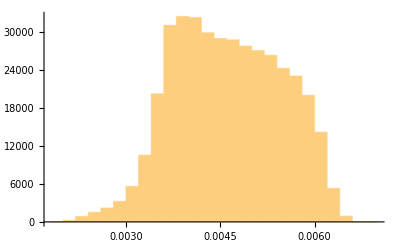

```mathematica
Histogram[Flatten[ImageData[tempImages[[1]]]]]
```